# The Walking Dead

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
GenerateAccumulatedCoordinates[coordinatesRange_,citiesNumber_]:=Module[{sampledCoordinates,citiesDummy,names,pops,cities},
(*Generate Random Coordinates*)
sampledCoordinates=citiesDummy = Accumulate[RandomReal[{-coordinatesRange,coordinatesRange}, {citiesNumber, 2}]];
names = ToString /@ Range[citiesDummy // Length];
pops = RandomInteger[1000, citiesDummy // Length];
cities = Transpose[{names, citiesDummy, pops}];
{sampledCoordinates,names,pops,cities}
]
SyllableToID[a_,labels_]:=Position[labels,a]
ConvertSyllablesToID[sample_,syllablesLabels_]:=Table[SyllableToID[sample[[i]],syllablesLabels],{i,1,Length[sample]}]//Flatten
InTuples[communitiesList_,syllablesLabels_]:=Module[{communitiesIndexes},communitiesIndexes=Map[(Map[Position[syllablesLabels,#]&,#]//Flatten)&,communitiesList];
Tuples[#,2]&/@communitiesIndexes]
ListPlotSong[sample_,syllablesLabels_,OptionsPattern[]]:=Module[{texts,g},texts=Graphics[Text[Style[ToString[#[[1]]],OptionValue[TextSize]],{(sample//Length)+10,#[[2]]},Automatic],AspectRatio->1]&/@({syllablesLabels,Range[syllablesLabels//Length]}//Transpose);
g=ListPlot[
If[OptionValue[Labeling]==True,Labeled[#[[1]],#[[2]]]&,Tooltip[#[[1]],#[[2]]]&]/@({ConvertSyllablesToID[sample,syllablesLabels],ToString/@sample}//Transpose),
ImageSize->OptionValue[ImageSize],
PlotStyle->Directive[Opacity[.75],PointSize[Medium]],
Filling->None,
AxesLabel->{"TimeStep","ID"},
PlotRange->{0,syllablesLabels//Length},
ImagePadding->50,
GridLines->Automatic,
GridLinesStyle->Directive[LightBlue],
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicksStyle->20
];
Show[g,texts,PlotRange->{0,(syllablesLabels//Length)+1}]
]
CalculateInOutRatio[inOutList_]:=(inOutList[[1]]/(inOutList[[1]]+inOutList[[2]]))
ListPlotSongWithCommunities[sample_,communities_,colors_,OptionsPattern[]]:=Module[{frequencyOutput,inOutTotals,labels2,individualCommunitiesInOutRatios,texts,connectionsRules,connectionsWithLabels,rect,rectangles,listPlot,sortedCommunities,wrappers,communitiesIDs,wrappersID},
frequencyOutput=GetTransitionsFrequencies[sample];
inOutTotals=GetCommunitiesInOutTransitionsFrequencies[frequencyOutput,communities,CountLoops->OptionValue[CountLoops]];
labels2=communities//Flatten//DeleteDuplicates;
sortedCommunities=Table[SortBy[i,Position[labels2,#]&],{i,communities}];
wrappers={(#//First)&/@sortedCommunities,(#//Last)&/@sortedCommunities}//Transpose;
communitiesIDs=Table[Position[labels2,#]&/@i//Flatten,{i,sortedCommunities}];
wrappersID={(#//First)&/@communitiesIDs,(#//Last)&/@communitiesIDs}//Transpose;
connectionsRules=wrappersID;
connectionsWithLabels=(UndirectedEdge[labels2[[#[[1]]]],labels2[[#[[2]]]]])&/@connectionsRules;
rect=Rectangle[{0.5,#[[1]]},{(sample//Length)+.5,#[[2]]},RoundingRadius->0]&/@connectionsRules;
rectangles=Graphics[
{
EdgeForm[Directive[Dashing[RandomReal[{0,0}]],Thickness[RandomReal[{.00175,.00175}]],Opacity[.2],colors[[#[[3]]]]]],Opacity[.2],colors[[#[[3]]]],#[[1]]
}
,ImagePadding->500]&/@({rect,Table[i[[1]]/(labels2//Length),{i,wrappersID}],Range[wrappersID//Length]}//Transpose);
individualCommunitiesInOutRatios=CalculateInOutRatio[#]&/@(inOutTotals//Transpose);
texts=Graphics[Text[Style[ToString[PaddedForm[#[[1]],{4,4}]],Bold,OptionValue[TextSize]],{(sample//Length)/2,#[[2]]+.35},Automatic],AspectRatio->1]&/@({individualCommunitiesInOutRatios,connectionsRules[[All,1]]}//Transpose);
listPlot=ListPlotSong[sample,labels2,ImageSize->OptionValue[ImageSize],Labeling->OptionValue[Labeling],TextSize->OptionValue[TextSize]];
Show[{listPlot,rectangles,texts}//Flatten]
]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/WalkingDead

RandomPointsPlot

RandomPointsMatrix

## Inputs

```mathematica
{vertexSize,vertexLabelSize}={.25,10};
(*Set the number of cities wanted, the x-y coordinates range to sample from, and the number of site types allowd*)
{citiesNumber,coordinatesRange,classesNumber}={20,500,15};
(*Assigns a class type to each point based on a random uniform distribution of probabilities and the number of types defined previously*)
(*Set a vector with the probabilities the walker has to stay in current node or move to the others. This vector is then rotated to generate the "partiteness" mask.*)
movementProbabilitiesVector=ConstantArray[0,classesNumber]//ReplacePart[#,{2->1,3->0}]&;
(*The penalizations matrix is a type-based transitions matrix to be used as mask down the road*)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,classesNumber}];
MatrixForm[penalizationsMatrix]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Generate Spatial Setting

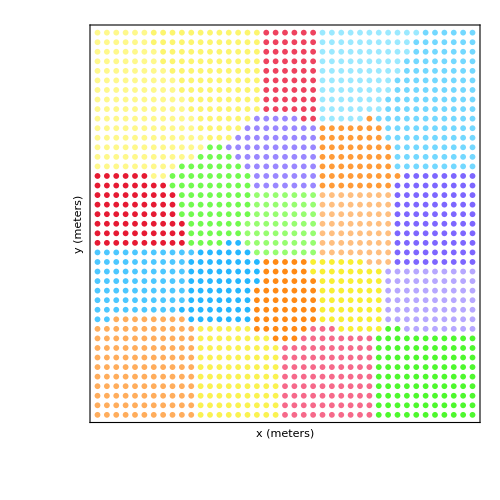

```mathematica
sampledCoordinates=Tuples[Range[-citiesNumber,citiesNumber],2];
distances = CalculateEuclideanDistances[sampledCoordinates];
cities=Transpose[{ToString/@Range[sampledCoordinates//Length],sampledCoordinates,ConstantArray[100,sampledCoordinates//Length]}];
(*Geo-Clustering*)
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
clustersStrings=Table[ToString/@Flatten[Position[cities[[All,2]],#]&/@clusteredCoordinates[[i]]],{i,1,clusteredCoordinates//Length}];
clustersIDs=Position[Map[ToExpression,clustersStrings,Infinity],#][[1,1]]&/@Range[Length[sampledCoordinates]];
(*Plots*)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clustersStrings])]]//Flatten//RandomSample;
ListPlot[clusteredCoordinates,PlotTheme->"RandomPointsPlot",ImageSize->500,PlotStyle->colors]
```

## Analyze

Map

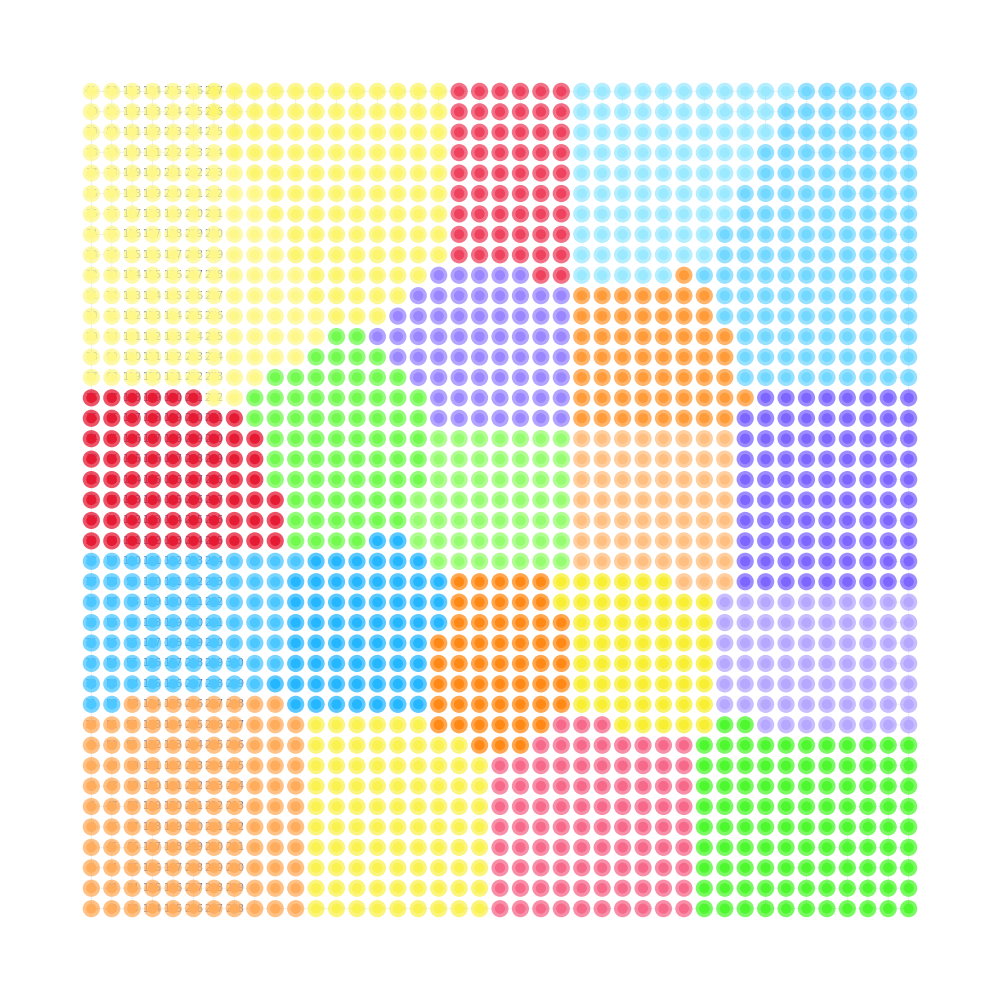

```mathematica
(*This "migration" is replacing the real kernel for the time being. It is based on the inverse of the distance to other nodes.*)
migration = CalculateMigrationProbabilities[distances, .05];
edgeshape2[e_,___]:={Arrowheads[{{.000001,.9}}],Arrow[e]}
stylesSwatch=Directive[Opacity[1],colors[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[clusteredCoordinates//Length];
stylesList=(ToString[#[[1]]]->stylesSwatch[[#[[2]]]])&/@Transpose[{Range[clustersIDs//Length],clustersIDs}];
map = GraphTransitionsFrequenciesWithMax[
  {
Chop[ReplacePart[migration,{i_,i_}->0]//LowerTriangularize,10^-2],
ToString /@ Range[Length[migration]]
   }, .15,
 VertexStyle ->stylesList,
VertexCoordinates ->sampledCoordinates,
VertexSize ->1vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize -> 1000,
LineThickness -> .0075,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both",
ImagePadding->50,
Epilog->Riffle[stylesList[[All,2]],(Disk[#,vertexSize]&/@sampledCoordinates)]
  ]
```

```mathematica
Export["00_clustering.pdf",map,ImageSize->2000,ImageResolution->500]
```

00_clustering.pdf

Mask Movement with Site-Types

```mathematica
(*If the transition between city types is not possible, or improbable, then mask it with the corresponding value. After that, normalize for the probabilities to still add up to one.*)
cityType=RandomChoice[Range[classesNumber],sampledCoordinates//Length]
{cityType[[1]],#}&/@cityType;
```

{14,10,12,15,7,15,8,6,5,3,11,9,2,1,2,10,13,10,11,14,7,2,4,5,1,3,8,15,7,1,15,14,14,8,7,7,8,6,1,2,9,2,6,13,8,1,5,6,2,11,15,10,7,4,2,4,10,8,1,9,8,5,5,15,6,1,9,7,3,2,15,2,11,10,3,2,5,9,11,14,4,10,8,4,12,6,7,14,9,9,9,12,5,6,7,14,10,10,4,6,12,11,12,6,4,3,15,6,15,8,2,15,12,9,2,12,13,13,5,5,3,15,13,11,3,9,3,7,9,9,15,1,1,11,8,14,7,11,11,10,14,9,9,6,15,10,1,10,15,11,10,10,7,7,4,11,15,7,12,4,12,5,15,6,7,8,5,11,4,6,7,14,14,4,7,12,5,10,1,13,2,6,5,14,10,8,5,15,1,15,5,12,1,11,2,14,1,5,1,9,13,15,2,2,7,11,2,2,2,5,10,6,2,1,14,6,2,9,8,1,15,3,12,8,7,7,6,11,12,9,11,8,10,8,9,11,14,1,2,13,1,4,12,15,5,10,5,4,6,15,2,15,1,5,11,10,6,11,9,5,14,7,6,6,4,15,5,8,1,14,9,1,5,2,14,12,1,12,13,7,15,4,11,12,10,12,5,4,8,4,5,1,1,5,8,8,5,2,1,1,4,14,10,5,6,3,3,4,5,8,13,14,15,7,4,4,8,4,3,5,5,1,15,9,8,15,8,3,4,6,11,5,4,5,5,2,9,8,3,15,8,2,10,4,3,15,12,1,8,7,8,12,12,3,3,11,8,3,15,3,2,1,12,10,1,9,3,9,1,15,10,10,6,6,5,15,13,14,9,15,2,8,5,13,10,13,14,6,13,15,6,5,2,5,4,7,11,11,14,9,4,13,10,3,4,11,1,13,13,5,1,6,8,11,4,11,15,8,1,15,12,14,2,7,15,3,12,13,1,11,6,10,4,8,5,1,7,3,15,10,8,4,5,10,5,4,13,7,5,9,10,1,12,15,14,3,1,15,14,2,2,7,13,14,10,11,1,3,9,3,11,9,9,10,12,11,5,12,7,3,9,13,9,1,9,6,5,6,1,14,9,10,2,3,9,14,5,9,6,5,7,10,11,14,8,13,15,5,8,1,3,15,10,12,7,15,2,5,5,15,5,15,12,8,10,10,14,5,9,8,6,13,14,4,3,7,2,8,8,11,15,6,7,7,4,7,14,7,12,7,5,12,4,10,8,14,10,9,13,5,1,8,13,9,5,10,3,14,11,10,10,13,3,2,5,9,12,4,10,14,1,6,9,10,15,12,11,14,15,15,6,15,4,7,9,3,2,15,6,3,10,14,11,8,7,4,7,6,8,9,14,7,3,15,10,15,4,14,15,12,14,2,11,6,3,8,6,10,3,5,10,9,10,13,15,11,15,3,5,10,9,11,6,15,15,13,12,5,5,8,3,5,15,3,13,2,8,10,15,5,7,14,10,14,10,15,13,15,10,10,3,4,13,4,9,7,10,14,15,12,14,11,3,15,6,10,4,4,8,10,6,3,3,5,7,1,9,14,9,4,3,9,15,12,9,14,13,15,15,14,3,8,8,3,15,3,12,13,11,6,15,9,2,10,1,5,4,5,6,1,8,8,8,1,5,7,3,1,13,2,2,5,3,3,9,1,10,13,1,14,12,9,14,4,13,10,7,1,5,15,1,8,5,15,9,12,12,1,13,4,10,7,13,5,9,8,13,8,5,11,5,3,4,3,13,9,11,15,10,6,4,11,12,15,4,4,5,5,1,5,11,4,1,8,6,4,6,13,4,1,3,13,13,3,10,2,15,1,3,8,4,4,10,11,12,11,9,12,7,5,6,15,8,14,2,12,10,10,7,5,5,9,15,5,11,7,15,6,1,7,4,2,9,1,9,10,13,8,14,3,3,5,3,4,1,2,6,5,9,13,7,1,1,7,3,9,7,5,13,8,13,3,4,14,10,5,6,9,10,8,3,4,4,1,5,6,8,10,1,13,14,14,6,6,8,6,13,9,3,8,3,3,4,3,3,8,10,15,9,8,11,10,11,7,8,13,2,10,4,8,10,10,3,12,11,9,5,2,1,14,5,10,3,14,12,14,11,13,15,4,5,2,6,2,15,4,4,14,3,5,4,10,6,10,12,8,11,15,9,7,8,6,5,14,4,14,5,1,3,2,5,1,15,14,4,11,10,13,11,10,11,1,9,7,13,3,3,7,4,11,5,15,3,6,12,6,10,14,5,4,14,13,8,7,15,3,2,9,2,15,3,11,13,14,9,8,11,6,9,7,3,4,12,14,4,7,13,2,15,12,2,2,8,1,15,10,11,13,13,11,14,11,9,10,3,6,1,1,4,12,9,12,13,11,13,5,7,15,4,13,14,12,4,15,5,12,8,2,7,10,14,15,2,11,9,15,14,1,13,12,14,3,10,5,3,4,9,10,13,4,12,11,11,7,8,9,3,4,5,11,6,3,4,14,7,4,10,2,11,6,7,12,8,3,11,8,1,5,6,15,3,1,4,3,1,11,6,7,8,11,5,13,7,1,5,3,10,1,11,8,15,1,4,3,8,4,4,1,1,6,7,10,12,1,11,5,13,12,7,1,14,2,13,14,8,8,2,8,2,12,4,15,1,7,6,6,12,11,4,10,9,7,8,9,7,15,12,15,14,6,2,1,6,1,8,1,5,3,10,10,14,9,2,14,14,1,7,13,12,2,7,2,1,4,15,6,10,6,6,10,3,2,2,13,13,13,7,10,15,1,5,4,4,12,14,6,6,12,7,9,15,10,8,13,13,14,14,3,8,1,8,4,5,8,3,15,13,14,2,15,8,11,10,3,14,11,4,11,4,9,12,8,11,15,13,11,2,9,11,13,5,4,4,7,2,2,15,13,11,5,10,6,10,4,4,14,9,8,1,9,11,5,10,12,7,5,8,10,3,6,8,6,10,8,1,8,9,14,6,5,8,5,7,5,14,3,6,15,8,9,9,6,10,1,1,2,6,12,6,10,4,5,4,3,4,1,11,4,4,9,15,10,11,13,10,6,12,2,2,9,11,13,1,1,8,7,12,4,7,10,13,15,15,11,14,3,3,7,5,10,15,2,10,14,7,7,15,12,3,11,8,5,13,15,6,10,2,14,4,5,7,9,11,11,9,11,8,8,11,8,5,12,7,12,2,13,15,6,7,9,4,12,12,8,1,6,10,14,10,3,4,4,10,1,4,15,10,4,7,2,9,11,12,6,3,12,5,13,13,13,9,1,3,9,4,7,8,6,14,8,12,15,7,9,13,9,10,4,7,6,11,5,12,14,12,14,12,6,9,9,5,3,5,11,15,2,7,8,1,6,10,14,14,3,12,12,12,5,3,7,5,1,1,7,13,10,15,3,4,11,11,4,4,3,6,11,12,14,3,15,10,5,14,6,4,7,9,6,3,15,11,6,4,1,3,7,15,13,8,12,6,12,8,5,1,1,4,10,5,12,2,1,8,15,3,13,5,4,6,3,2,1,2,11,8,3,15,9,4,2,14,5,5,1,7,6,13,2,10,10,14,8,9,3,13,5,7,7,2,15,5,11,7,3,10,7,6,15,1,2,10,6,13,4,12,1,10,9,11,10,4,9,10,4,5,7,9,6,3,10,3,8,9,12,6,2,11,3,3,3,8,11,10,15,13,3,3,4,2,11,15,6,9,3,14,10,3,3,1,10,2,12,5,3,13,9,1,9,10,14,8,5,1,5,8,4,14,14,2,6,6}

```mathematica
penalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
normalizedMaskedMatrix=(#/Total[#])&/@(penalizationsMask*migration);
(*Plots*)
penalizationsMaskPlot=penalizationsMask//MatrixPlot[#,ColorFunction -> "LakeColors", ImageSize ->500/2]&;
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/classesNumber]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
normalizedMaskedMatrixPlot=normalizedMaskedMatrix//MatrixPlot[#,ColorFunction->"LakeColors"]&;
```

Movement Network

```mathematica
edgeshape2[e_,___]:={Arrowheads[{{.015,.75}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .35,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize ->vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize->1000,
LineThickness->.005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both",
ImagePadding->50
  ];
Export["01_Movement.pdf",%,ImageSize->2000,ImageResolution->500]
```

01_Movement.pdf

Markov

```mathematica
kernel=normalizedMaskedMatrix;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
MarkovProcessProperties[markov,"LimitTransitionMatrix"][[1]];
```

```mathematica
markov=DiscreteMarkovProcess[initialState,kernel];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
histogram=SmoothHistogram[markovPDF,Frame->True,FrameStyle->Black,PlotStyle->Thickness[.005],ImageSize->1000,Filling->Bottom];
matrix=MatrixPlot[{markovPDF},Frame->False,FrameStyle->Directive[Black,Thick],ColorFunction->ColorData[{"LakeColors","Reverse"}],FrameTicks->{None,All},ImageSize->1000];
violinPDF=DistributionChart[markovPDF,ChartStyle->"LakeColors",AspectRatio->.2,Frame->False,BarOrigin->Left,ImageSize->1000];
PDFandCDF=ListLinePlot[{Accumulate[markovPDF//Sort//Reverse],100*markovPDF//Sort},
Frame->True,
FrameStyle->Thick,
PlotStyle->Thickness[.005],
ImageSize->1000,
PlotLabel->("[Max: "<>ToString[Max[markovPDF]]<>"]::["<>"Mean: "<>ToString[Mean[markovPDF]]<>"]::["<>"Min: "<>ToString[Mean[markovPDF]]<>"]"<>"]::["<>"SD: "<>ToString[StandardDeviation[markovPDF]]<>"]")
];
Grid[{{violinPDF},{matrix},{PDFandCDF}}];
Export["03_MarkovStationary01.pdf",%]
(*MatrixPlot[{tally[[All,2]]},ColorFunction->ColorData[{"LakeColors","Reverse"}],ImageSize->1000]*)
```

03_MarkovStationary01.pdf

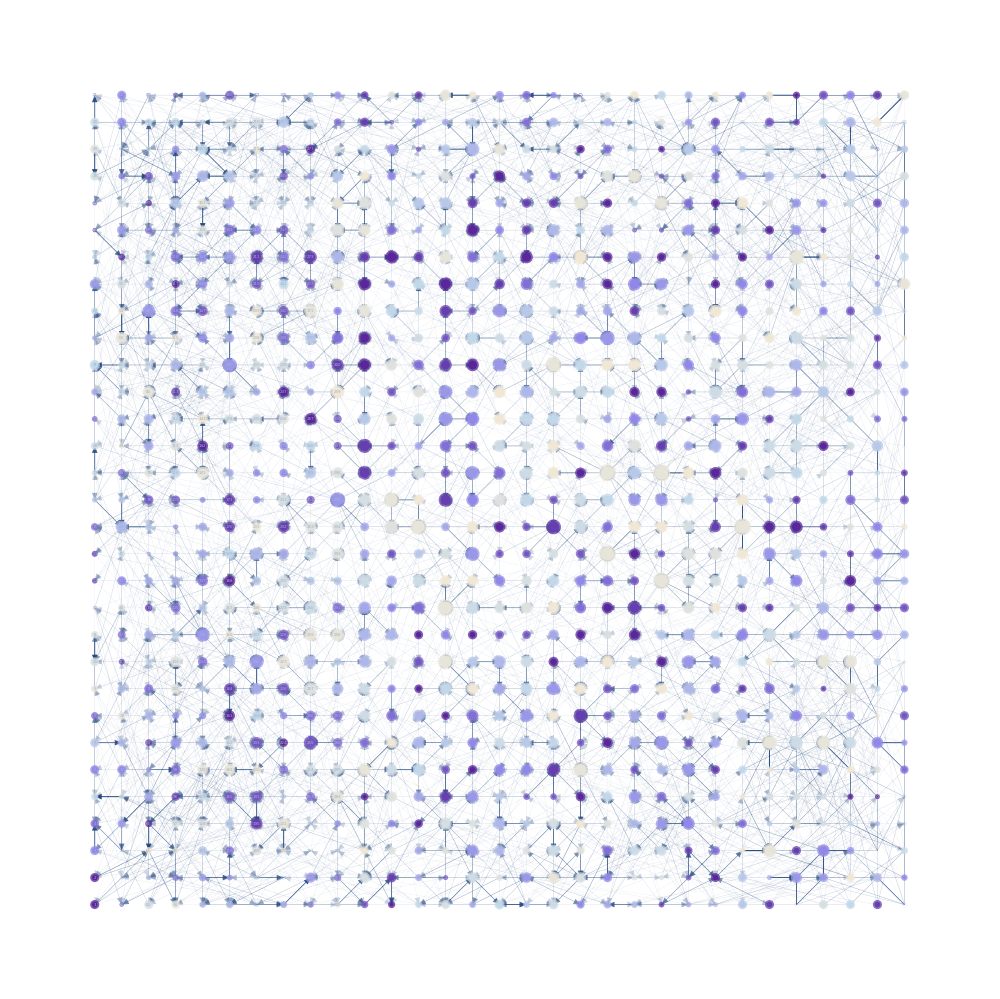

03_MarkovStationary02.png

```mathematica
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.0025]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
edgeshape2[e_,___]:={Arrowheads[{{.0025,.9}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .15,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize -> Thread[VertexList[graph]->.25*Log[0+7.5*Rescale[markovPDF]]],
VertexLabelStyle->.001,
ImageSize->1000,
LineThickness->.0005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both",
ImagePadding->10
  ]
Export["03_MarkovStationary02.png",%,ImageSize->3000,ImageResolution->300]
```

```mathematica
sampledCoordinates//Length
```

961